```mathematica
Sort[
Select[
Monitor[
Flatten[
Table[
With[
{g=Graph[plantri[[k]]]},
Table[
{k,v1,
With[
{counts=Table[VertexDegree[g,v2],{v2,VertexList[VertexDelete[NeighborhoodGraph[g,v1],v1]]}]},
{Length[Select[counts,#==5&]],counts, Total[counts]}]

}
,{v1, Select[VertexList[g],VertexDegree[g,#]==5&]}
]
],{k,1,100000}
],
1],
{k,v1}
],
#[[3,1]]==0 &
],
#1[[3,3]]>#2[[3,3]]&]
```

{{88151,18,{0,{12,7,7,6,6},38}},{99440,13,{0,{12,7,6,6,6},37}},{99238,19,{0,{12,7,6,6,6},37}},{97837,13,{0,{11,8,6,6,6},37}},{97835,14,{0,{7,10,8,6,6},37}},{97826,19,{0,{10,8,6,7,6},37}},{97068,13,{0,{12,6,6,7,6},37}},{97029,9,{0,{6,11,6,7,7},37}},{96933,13,{0,{13,6,6,6,6},37}},{96749,14,{0,{11,7,7,6,6},37}},{96722,8,{0,{7,10,8,6,6},37}},8230,{523,17,{0,{6,6,6,6,6},30}},{389,12,{0,{6,6,6,6,6},30}},{388,12,{0,{6,6,6,6,6},30}},{387,13,{0,{6,6,6,6,6},30}},{386,15,{0,{6,6,6,6,6},30}},{385,9,{0,{6,6,6,6,6},30}},{384,8,{0,{6,6,6,6,6},30}},{383,8,{0,{6,6,6,6,6},30}},{197,8,{0,{6,6,6,6,6},30}},{140,15,{0,{6,6,6,6,6},30}}}
 |  |  |  |

```mathematica
Length[plantri]
```

100000

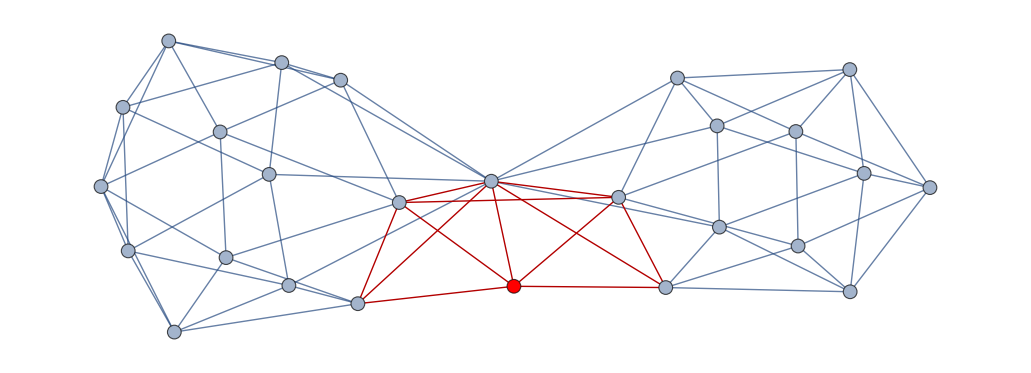

```mathematica
With[
{k=88151,v=18},
Graph[plantri[[k]],  VertexStyle->{v -> Red}, GraphHighlight->EdgeList[NeighborhoodGraph[Graph[plantri[[k]]],v]]]
]
```

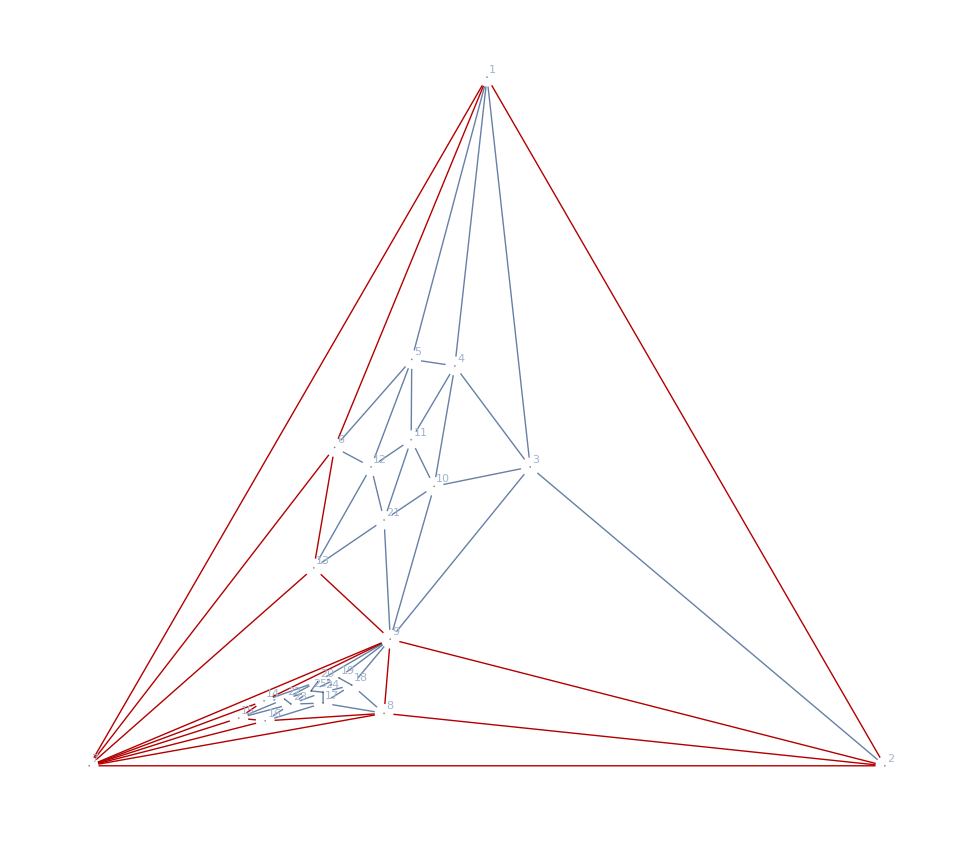

```mathematica
With[
{k=24534,v=7},
Graph[plantri[[k]], VertexLabels->"Name",GraphLayout->"TutteEmbedding",VertexSize->Tiny, VertexStyle->{v -> Red}, GraphHighlight->EdgeList[NeighborhoodGraph[Graph[plantri[[k]]],v]]]
]
```

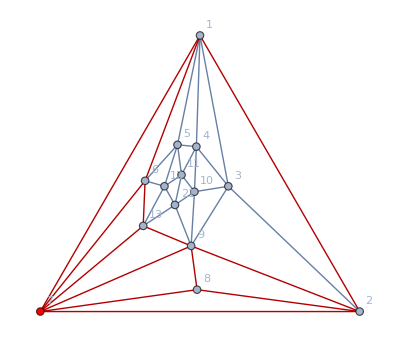

```mathematica
pruned=With[
{k=24534,v=7},
VertexDelete[Graph[plantri[[k]], VertexLabels->"Name",GraphLayout->"TutteEmbedding", VertexStyle->{v -> Red}, GraphHighlight->EdgeList[NeighborhoodGraph[Graph[plantri[[k]]],v]]],{14,15,16,22,23,17,24,25,20,19,18}]
]
```

```mathematica
VertexList[pruned]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,21}

```mathematica
VertexCount[pruned]
```

14

```mathematica
FindGraph[pruned,1,300000]
```

111445

```mathematica
FindPlantri[pruned,1,100000]
```

-1

```mathematica
GraphSignature2[pruned]
```

7-6-6-5-5-5-5-5-5-5-5-5-5-3

```mathematica
ChromaticPolynomial[pruned,4]
```

336

```mathematica
FindPlantri[Graph[plantri[[24534]]],1,100000]
```

24534

```mathematica
VertexCount[sub]
```

14

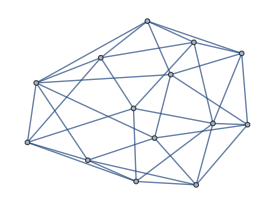

```mathematica
sub=NeighborhoodGraph[Graph[plantri[[24534]]],{14,15,16,22,23,17,24,25,20,19,18}]
```

```mathematica
FindPlantri[sub,1,100000]
```

2

```mathematica
ChromaticPolynomial[sub,4]
```

480

```mathematica
GraphSignature2[sub]
```

6-6-5-5-5-5-5-5-5-5-5-5-5-5

```mathematica
ChromaticPolynomial[Graph[plantri[[24534]]],4]
```

6720

```mathematica
sub
```

```mathematica
GraphSignature2[Graph[plantri[[24534]]]]
```

11-9-6-6-6-5-5-5-5-5-5-5-5-5-5-5-5-5-5-5-5-5-5-5-5

```mathematica
TableForm[FactorInteger[{336/24,480/24,336,480,24, 336*480/24,6720}], TableDepth->2]
```

{2,1} | {7,1} |  | 
{2,2} | {5,1} |  | 
{2,4} | {3,1} | {7,1} | 
{2,5} | {3,1} | {5,1} | 
{2,3} | {3,1} |  | 
{2,6} | {3,1} | {5,1} | {7,1}
{2,6} | {3,1} | {5,1} | {7,1}

```mathematica
MaximalPlanarQ[sub]
```

True

```mathematica
VertexCount[sub]
```

14

```mathematica
FindGraph[sub,50000,300000]
```

279676

```mathematica
VertexCount[Graph[plantri[[24534]]]]
```

25

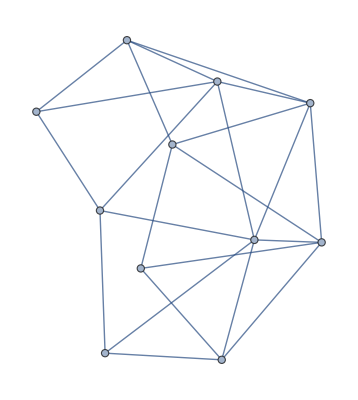

```mathematica
sub2=VertexDelete[NeighborhoodGraph[Graph[plantri[[24534]]],{14,15,16,22,23,17,24,25,20,19,18}],{7,8,9}]
```

```mathematica
MaximalPlanarQ[sub2]
```

False

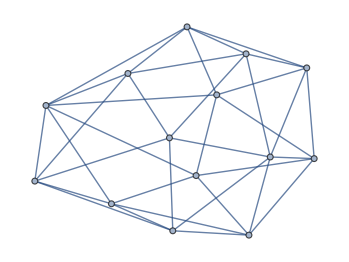

```mathematica
Graph[sub,GraphLayout->"TutteEmbedding"]
```

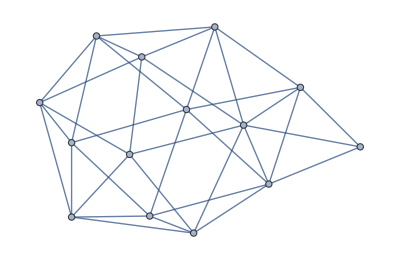

```mathematica
ReadGrof[111445]
```